The file format for the file is a list of points with seven entries each. The entries contain the following:

1) {x, y}, the parameter values over which the loop was iterated

2) {M1, M2, M3, M0, Mtau, 
MQ, MNR, tanβ, v, vevS, 
Atop, Abtm, Atau, An11, An12,
 An13, AlambdaN, Yn11, Yn12, Yn13, 
 lambda, lambdaN, kappa, PhisPI, Phi2PI, 
 ksi, Alambda, Akappa}, the input parameters
 
3) {χN-mass(5),  χC-mass(2), H+-mass(2), ν-mass(4), snu-mass(8), 
H0-mass(6), slep-mass(6), sup-mass(2), sdn-mass(2), stp-mass(2), 
sbt-mass(2)}, the mass eigenvalues, each of these is a vector in itself with the dimension noted in parentheses.

4) {χNre(5x5), χNim(5x5), 
χC-Ure(2x2),  χCU-im(2x2), χCV-re(2x2), χCV-im(2x2),  
νre(4x4), νim(4x4), 
H0(6x6), 
snu(8x8), 
slepCre(6x6), slepCim(6x6), 
sdown-re(2x2), sdown-im(2x2), sup-re(2x2), sup-im(2x2), stop-re(2x2), stop-im(2x2), sbottom-re(2x2), sbottom-im(2x2),
H+-(2x2)}, the mixing matrices, each of these is a nxn matrix with the dimensions noted in parentheses

5) {contribution in %, absolute contribution, channel}, the contributing channels to omega

6) {omega, CDM candidate name, Xf}, self explanatory

7) {cross section in pb, input channel, output channel}, cross sections for selected channels

8) CDM nucleon magic (amp = micromegas Amplitude, cs=cross section [pb])
{{n-cdm SI amp, n-anti-cdm SI amp, n-cdm SD amp, n-anti-cdm SD amp}, 
  {p-cdm SI amp, p-anti-cdm SI amp, p-cdm SD amp, p-anti-cdm SD amp}, 
  {n-cdm SI cs, n-anti-cdm SI cs, n-cdm SD cs, n-anti-cdm SD cs}, 
  {p-cdm SI cs, p-anti-cdm SI cs, p-cdm SD cs, p-anti-cdm SD cs}}

Load the data.

```mathematica
file1=<<"/Users/ruppell/Math/temp/output-fig8L.txt";
label1="Fig 8 left";
```

```mathematica
file4=<<"/Users/ruppell/Math/temp/output-fig8R.txt";
label2="Fig 8 right";
```

Split the data into two sets, one with Relic Density (RD) between 0.1 and 0.12 and another with RD outside that range

```mathematica
file2=Select[file1,(#[[6,1]]<0.1232&&#[[6,1]]>0.1008)&];
file3=Select[file1,(#[[6,1]]>0.1232||#[[6,1]]<0.1008)&];
```

```mathematica
file5=Select[file4,(#[[6,1]]<0.1232&&#[[6,1]]>0.1008)&];
file6=Select[file4,(#[[6,1]]>0.1232||#[[6,1]]<0.1008)&];
```

Build the {x,y,z} triplets for the plots.

```mathematica
xaxel0=Flatten@file2[[All,2,17]];
yaxel0=Flatten@file2[[All,2,22]];
zaxel0=Flatten@file2[[All,6,1]];
waxel0=Flatten@file2[[All,2,7]];

xaxel1=Flatten@file3[[All,2,17]];
yaxel1=Flatten@file3[[All,2,22]];
zaxel1=Flatten@file3[[All,6,1]];
waxel1=Flatten@file3[[All,2,7]];
```

```mathematica
xaxel2=Flatten@file5[[All,2,17]];
yaxel2=Flatten@file5[[All,2,22]];
zaxel2=Flatten@file5[[All,6,1]];
waxel2=Flatten@file5[[All,2,7]];

xaxel3=Flatten@file6[[All,2,17]];
yaxel3=Flatten@file6[[All,2,22]];
zaxel3=Flatten@file6[[All,6,1]];
waxel3=Flatten@file6[[All,2,7]];
```

```mathematica
dataRDacc1=Transpose@{xaxel0,yaxel0,Log[10,zaxel0]};
dataMRacc1=Transpose@{xaxel0,yaxel0,waxel0};
data2Dacc1=Transpose@{xaxel0,yaxel0};

dataRDdis1=Transpose@{xaxel1,yaxel1,Log[10,zaxel1]};
dataMRdis1=Transpose@{xaxel1,yaxel1,waxel1};
data2Ddis1=Transpose@{xaxel1,yaxel1};
```

```mathematica
dataRDacc2=Transpose@{xaxel2,yaxel2,Log[10,zaxel2]};
dataMRacc2=Transpose@{xaxel2,yaxel2,waxel2};
data2Dacc2=Transpose@{xaxel2,yaxel2};

dataRDdis2=Transpose@{xaxel3,yaxel3,Log[10,zaxel3]};
dataMRdis2=Transpose@{xaxel3,yaxel3,waxel3};
data2Ddis2=Transpose@{xaxel3,yaxel3};
```

Plot the lambda_N, Alambda_N plane with MNR as the z-axis. Orange points are nor OK for RD, blue points have the correct RD.

```mathematica
pMR1=ListPointPlot3D[{dataMRacc1,dataMRdis1},PlotRange->{{-1000,-200},{0.,0.05},{0,500}},
BoxRatios->{1,1,1},PlotStyle->{Blue,Orange},ImageSize->400,PlotLabel->label1,
AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"],Subscript["M",Subscript["N","R"]]}];
```

```mathematica
pMR2=ListPointPlot3D[{dataMRacc2,dataMRdis2},PlotRange->{{-1000,-200},{0.,0.05},{0,500}},
BoxRatios->{1,1,1},PlotStyle->{Blue,Orange},ImageSize->400,PlotLabel->label2,
AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"],Subscript["M",Subscript["N","R"]]}];
```

```mathematica
TableForm@{{pMR1,pMR2}}
```

-Graphics3D- | -Graphics3D-

Plot the lambda_N, Alambda_N plane with RD as the z-axis. Coloring the same as previously.

```mathematica
pRD1=ListPointPlot3D[{dataRDacc1,dataRDdis1},PlotRange->{{-1000,-200},{0.,0.05},{-3,3}},
BoxRatios->{1,1,1},PlotStyle->{Blue,Orange},ImageSize->400,PlotLabel->label1,
AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"],"Log(Ω_Nh^2)"}];
```

```mathematica
pRD2=ListPointPlot3D[{dataRDacc2,dataRDdis2},PlotRange->{{-1000,-200},{0.,0.05},{-3,3}},
BoxRatios->{1,1,1},PlotStyle->{Blue,Orange},ImageSize->400,PlotLabel->label2,
AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"],"Log(Ω_Nh^2)"}];
```

```mathematica
TableForm@{{pRD1,pRD2}}
```

-Graphics3D- | -Graphics3D-

A 2D projection of the RD OK points in the lambda_N, Alambda_n plane.

```mathematica
p2D1=ListPlot[data2Dacc1,PlotRange->{{-1000,-200},{0.,0.05}},AspectRatio->1,ImageSize->400,PlotLabel->label1,AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"]}];
```

```mathematica
p2D2=ListPlot[data2Dacc2,PlotRange->{{-1000,-200},{0.,0.05}},AspectRatio->1,ImageSize->400,PlotLabel->label2,AxesLabel->{Subscript["A",Subscript["λ","N"]],Subscript["λ","N"]}];
```

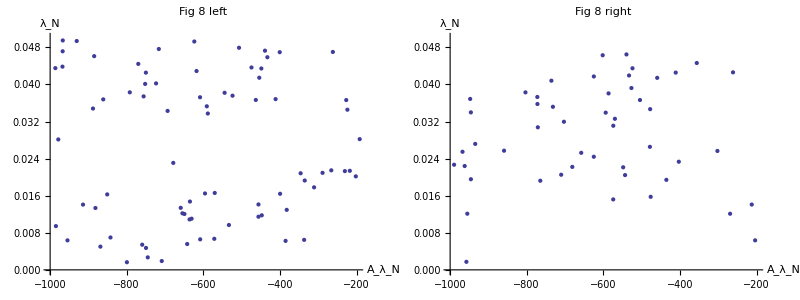

```mathematica
TableForm@{{p2D1,p2D2}}
```